```mathematica
ClearAll[s,h,u,L]
```

```mathematica
(* This should be the exact, non-perturbative result for what you call I(k) in your latest notes.  Here what I have done is use the asymptotic expansions to leading order for both ArcTan and Sqrt[1+y^2].  Beyond that I have not approximated the integral.  Note that I can only do this integral in closed form in the α=1 case, which is what is shown here. *)

Integrate[Exp[I (s-u) y] Exp[I s h π/2] Exp[-h Abs[s] y],{y,L/2,Infinity},Assumptions->{L∈Reals,L>0,s∈Reals,Abs[s]>0,h>0,u∈Reals,α∈Reals,α≥1,α≤2}]
```

(ⅈ ⅇ^(1/2 ⅈ (h π s+L (s-u)+ⅈ h L Abs[s])))/(s-u+ⅈ h Abs[s])

```mathematica
(* This should be the exact, non-perturbative result for what you call I(k) in your latest notes *)Integrate[Exp[I (s-u) y] Exp[-I s h π/2] Exp[h Abs[s] y],{y,-Infinity,-L/2},Assumptions->{L∈Reals,L>0,s∈Reals,Abs[s]>0,h>0,u∈Reals,α∈Reals,α≥1,α≤2}]
```

-(ⅈ ⅇ^(-1/2 ⅈ (h π s+L (s-u)-ⅈ h L Abs[s])))/(s-u-ⅈ h Abs[s])

```mathematica
myresult[s_,u_] := 2 Re[(ⅈ ⅇ^(1/2 ⅈ (h π s+L (s-u)+ⅈ h L Abs[s])))/(s-u+ⅈ h Abs[s])]
smallarg[s_,u_] := 2 Re [Exp[I (s-u) L/2] Exp[I s h π/2]/(α h^(1/α) Abs[s])  Gamma[α^(-1),h (Abs[s] L/2)^α]]
largearg[s_,u_] := 2 Re [- Exp[-h Abs[s]^α (L/2)^α + I(s-u) L/2 + I s h π/2] (1/(I (s-u)) + α h Abs[s]^α (L/2)^(α-1)/(s-u)^2)]
```

```mathematica
α=1.0;
L=12.8;
h=0.01;
```

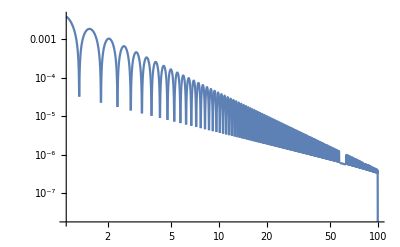

```mathematica
(* Here I am fixing s to be 0.1 because this is where things go haywire for me in the "kernel" matrix K(s,u,h) --- when s is small *)
(* The log log plot below certainly shows that your "large" |s-u| expansion is working! *) 
LogLogPlot[Abs[myresult[0.1,u] - largearg[0.1,u]],{u,1.1,100},PlotRange->All]
```

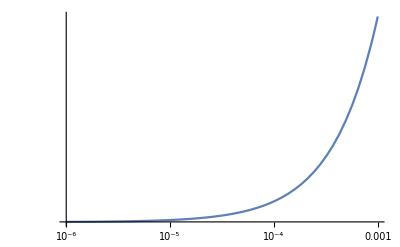

```mathematica
(* Here I am fixing s to be 0.1 because this is where things go haywire for me in the "kernel" matrix K(s,u,h) --- when s is small *)
(* The log log plot indicates that the "small" |s-u| expansion is very different from the "exact" answer I have been using.  Not sure why.  *)
LogLogPlot[Abs[myresult[0.1,u] - smallarg[0.1,u]],{u,0.000001,0.001},PlotRange->All]
```

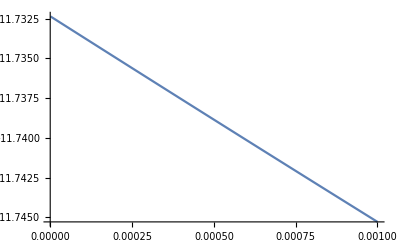

```mathematica
Plot[myresult[0.1,u],{u,0.000001,0.001},PlotRange->All]
```

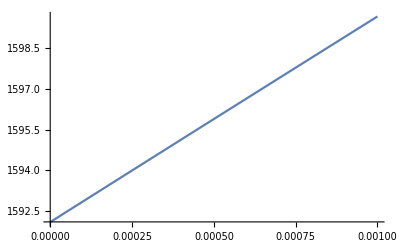

```mathematica
Plot[smallarg[0.1,u],{u,0.000001,0.001},PlotRange->All]
```